```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumpsall={d>0,m>0,vperp>0,ΔPE∈Reals,κpar0>1/2,Tpar0>0,Tperp0>0,κperp0>1,Tperp0>0,n0>0};
assumps={m>0,κpar0>1/2,Tpar0>0,Ε∈Reals};
assumps2={m>0,κpar0>1/2,Tpar0>0,Ε∈Reals,Ε+Tpar0 κpar0≥0};

Ipar=FullSimplify[Integrate[(1+(1/2*m*vpar^2+Ε)/(κpar0*Tpar0))^(-(1+κpar0)),{vpar,-Infinity,Infinity},Assumptions->assumps2],assumps2]
FullSimplify[Ipar==Sqrt[(2*Pi*Tpar0)/(m*κpar0)]*(Gamma[1/2+κpar0]*(1+Ε/(κpar0*Tpar0))^(-(1/2+κpar0)))/Gamma[κpar0],assumps2]
```

(√(2 π) Tpar0 ((Tpar0 κpar0)/(Ε+Tpar0 κpar0))^κpar0 Gamma[1/2+κpar0])/(√(m (Ε+Tpar0 κpar0)) Gamma[κpar0])

True

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={α>0,β>2,γ>0,η>1};


FullSimplify[Integrate[x*(1+α*x)^-β*(1+γ*x)^-η,{x,0,Infinity},Assumptions->assumps],assumps]
```

(-(π α^(-2+η) γ^β (-α+γ)^(1-β-η) (α (-1+β)+γ (-1+η)) Csc[π η] Gamma[-2+β+η])/(Gamma[β] Gamma[η])+(γ+((α-α β+γ-γ η) Hypergeometric2F1[1,β,3-η,α/γ])/(-2+η))/((α-γ) (-1+η)))/γ^2

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Gamma[0]
Gamma[1]
Gamma[2]
Gamma[3]
Gamma[4]
```

Remove::rmnsm: There are no symbols matching "Global`*".

ComplexInfinity

1

1

2

6

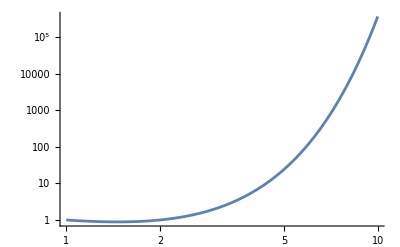

```mathematica
LogLogPlot[Gamma[x],{x,1,10}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*assumps={κpar0>1/2,κperp0>1,Tpar0>0,Tperp0>0,ΔPE/(κpar0*Tpar0)>-1,ΔPE∈Reals,n0>0,m>0};*)
assumps={κpar0>1/2,κperp0>1,Tpar0>0,Tperp0>0,n0>0,m>0};
FullSimplify[Solve[n0==C0*2*Pi*Integrate[vperp0*(1+(m*vpar0^2)/(2*κpar0*Tpar0))^(-1-κpar0)*(1+(m*vperp0^2)/(2*κperp0*Tperp0))^(-1-κperp0),{vperp0,0,Infinity},{vpar0,-Infinity,Infinity},Assumptions->assumps],C0],assumps]
```

{{C0→(n0 Gamma[1+κpar0])/(2 √2 π^(3/2) Tperp0 √((Tpar0 κpar0)/m^3) Gamma[1/2+κpar0])}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κpar0>1/2,κperp0>1,Tpar0>0,Tperp0>0,ΔPE/(κpar0*Tpar0)>-1,ΔPE∈Reals,n0>0,m>0,d>1};
C0=(n0 Gamma[1+κpar0])/(2 √2 π^(3/2) Tperp0 √((Tpar0 κpar0)/m^3) Gamma[1/2+κpar0]);
moment[num_]:=2*Pi*C0*Sqrt[2*(Pi*Tpar0)/(m*κpar0)]*Gamma[κpar0+1/2]/Gamma[κpar0]*(1+ΔPE/(κpar0*Tpar0))^(-(1/2+κpar0))*1/2*((2*κpar0*Tpar0*d)/m)^(num/2+1)*Beta[1+num/2,κpar0+κperp0+1/2-num/2]*Hypergeometric2F1[1+num/2,1/2+κpar0,κpar0+κperp0+3/2,1-δ];
FullSimplify[moment[0],assumps]//TraditionalForm
```

1/Tperp0 d n0 (κpar0 Tpar0)^(κpar0+3/2) 1κpar0+κperp0+1/2 (ΔPE+κpar0 Tpar0)^(-κpar0-1/2) 1κpar0+1/2κpar0+κperp0+3/21-δ

```mathematica
Gamma[3]
```

2

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumpsall={d>0,m>0,vperp>0,ΔPE∈Reals,κpar0>1/2,Tpar0>0,Tperp0>0,κperp0>1,Tperp0>0,n0>0};
assumps={m>0,κpar0>1/2,Tpar0>0,Ε∈Reals};
assumps2={m>0,κpar0>1/2,Tpar0>0,Ε∈Reals,Ε+Tpar0 κpar0≥0,num>0};

Ipar=FullSimplify[Integrate[vpar^num*(1+(1/2*m*vpar^2+Ε)/(κpar0*Tpar0))^(-(1+κpar0)),{vpar,-Infinity,Infinity},Assumptions->assumps2],assumps2]
FullSimplify[Ipar==(2^(1/2 (-1+num)) (1+(-1)^num) m^(-1/2-num/2) Tpar0 κpar0 (Tpar0 κpar0)^κpar0 (Ε+Tpar0 κpar0)^(1/2 (-1+num-2 κpar0)) Gamma[(1+num)/2] Gamma[1/2-num/2+κpar0])/Gamma[1+κpar0],assumps2]
```

ConditionalExpression[(2^(1/2 (-1+num)) (1+(-1)^num) m^(-1/2-num/2) Tpar0 κpar0 (Tpar0 κpar0)^κpar0 (Ε+Tpar0 κpar0)^(1/2 (-1+num-2 κpar0)) Gamma[(1+num)/2] Gamma[1/2-num/2+κpar0])/Gamma[1+κpar0], num<1+2 κpar0]

ConditionalExpression[True, num<1+2 κpar0]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumpsall={d>0,m>0,vperp>0,ΔPE∈Reals,κpar0>1/2,Tpar0>0,Tperp0>0,κperp0>1,Tperp0>0,n0>0};
assumps={m>0,κpar0>1/2,Tpar0>0,Ε∈Reals};
assumps2={m>0,κpar0>1/2,Tpar0>0,Ε∈Reals,Ε+Tpar0 κpar0≥0,num>0};


FullSimplify[(2^(1/2 (-1+num)) (1+(-1)^num) m^(-1/2-num/2) Tpar0 κpar0 (Tpar0 κpar0)^κpar0 (Ε+Tpar0 κpar0)^(1/2 (-1+num-2 κpar0)) Gamma[(1+num)/2] Gamma[1/2-num/2+κpar0])/Gamma[1+κpar0]==(2^(1/2 (-1+num)) (1+(-1)^num) m^(-1/2-num/2) (Tpar0 κpar0)^((num+1)/2) (1+Ε/(Tpar0 κpar0))^(1/2 (-1+num-2 κpar0)) Gamma[(1+num)/2] Gamma[1/2-num/2+κpar0])/Gamma[1+κpar0],assumps2]
```

True

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κpar>1/2,κperp>1,Tpar>0,Tperp>0,n>0,m>0,num>0};
c=(n Gamma[1+κpar])/(2 √2 π^(3/2) Tperp √((Tpar κpar)/m^3) Gamma[1/2+κpar]);
FullSimplify[c*2*Pi*Integrate[vperp^(num+1)*(1+(m*vpar^2)/(2*κpar*Tpar))^(-1-κpar)*(1+(m*vperp^2)/(2*κperp*Tperp))^(-1-κperp),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
FullSimplify[c*2*Pi*Integrate[vperp*vpar^num*(1+(m*vpar^2)/(2*κpar*Tpar))^(-1-κpar)*(1+(m*vperp^2)/(2*κperp*Tperp))^(-1-κperp),{vperp,0,Infinity},{vpar,-Infinity,Infinity},Assumptions->assumps],assumps]
```

ConditionalExpression[(2^(num/2) n ((Tperp κperp)/m)^(num/2) Gamma[1+num/2] Gamma[-num/2+κperp])/Gamma[κperp], num<2 κperp]

(2^(-1+num/2) (1+(-1)^num) n ((Tpar κpar)/m)^(num/2) Gamma[(1+num)/2] Gamma[1/2-num/2+κpar])/(√π Gamma[1/2+κpar])

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κpar>1/2,κperp>1,Tpar>0,Tperp>0,n>0,m>0,num>0};
momentperp[num_]:=(2^(num/2)  ((Tperp κperp)/m)^(num/2) Gamma[1+num/2] Gamma[-num/2+κperp])/Gamma[κperp];
momentpar[num_]:=(2^(-1+num/2) (1+(-1)^num)  ((Tpar κpar)/m)^(num/2) Gamma[(1+num)/2] Gamma[1/2-num/2+κpar])/(√π Gamma[1/2+κpar]);
FullSimplify[momentperp[0],assumps]
FullSimplify[momentperp[1],assumps]
FullSimplify[momentperp[2],assumps]
FullSimplify[momentperp[3],assumps]
FullSimplify[momentperp[4],assumps]
FullSimplify[momentpar[0],assumps]
FullSimplify[momentpar[1],assumps]
FullSimplify[momentpar[2],assumps]
FullSimplify[momentpar[3],assumps]
FullSimplify[momentpar[4],assumps]
```

1

(√(π/2) √((Tperp κperp)/m) Gamma[-1/2+κperp])/Gamma[κperp]

-(2 Tperp κperp)/(m-m κperp)

(3 √(π/2) ((Tperp κperp)/m)^(3/2) Gamma[-3/2+κperp])/Gamma[κperp]

(8 Tperp^2 κperp^2 Gamma[-2+κperp])/(m^2 Gamma[κperp])

1

0

-(2 Tpar κpar)/(m-2 m κpar)

0

(12 Tpar^2 κpar^2)/(m^2 (3+4 (-2+κpar) κpar))

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κpar>1/2,κperp>1,Tpar>0,Tperp>0,κpar0>1/2,κperp0>1,Tpar0>0,Tperp0>0,m>0,num>0,δ>0,n0>0};
C0=(n0 Gamma[1+κpar0])/(2 √2 π^(3/2) Tperp0 √((Tpar0 κpar0)/m^3) Gamma[1/2+κpar0]);
momentperp0[num_]:=2*Pi*C0*Sqrt[2*(Pi*Tpar0)/(m*κpar0)]*Gamma[κpar0+1/2]/Gamma[κpar0]*(1+ΔPE/(κpar0*Tpar0))^(-(1/2+κpar0))*1/2*((2*κperp0*Tperp0*d)/m)^(num/2+1)*Beta[1+num/2,κpar0+κperp0+1/2-num/2]*Hypergeometric2F1[1+num/2,1/2+κpar0,κpar0+κperp0+3/2,1-δ];
Ipar0[num_]:=2^((num-1)/2)*((-1)^num+1)*m^((-(num+1))/2)*Gamma[(num+1)/2]*Gamma[(1-num)/2+κpar0]/Gamma[κpar0+1]*(κpar0*Tpar0)^((num+1)/2);
momentpar0[num_]:=2*Pi*C0*Ipar0[num]*(1+ΔPE/(κpar0*Tpar0))^(-κpar0+(num-1)/2)*1/2*((2*κperp0*Tperp0*d)/m)*Beta[1,κpar0+κperp0+(1-num)/2]*Hypergeometric2F1[1,(1-num)/2+κpar0,κpar0+κperp0+1+(1-num)/2,1-δ];
FullSimplify[momentperp0[0],assumps]
FullSimplify[momentperp0[1],assumps]
FullSimplify[momentperp0[2],assumps]
FullSimplify[momentperp0[3],assumps]
FullSimplify[momentperp0[4],assumps]
FullSimplify[momentpar0[0],assumps]
FullSimplify[momentpar0[1],assumps]
FullSimplify[momentpar0[2],assumps]
FullSimplify[momentpar0[3],assumps]
FullSimplify[momentpar0[4],assumps]
```

d n0 (1+ΔPE/(Tpar0 κpar0))^(-1/2-κpar0) κperp0 Beta[1,1/2+κpar0+κperp0] Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ]

√2 d^(3/2) n0 (Tpar0 κpar0)^κpar0 (ΔPE+Tpar0 κpar0)^(-1/2-κpar0) √((Tpar0 Tperp0 κpar0 κperp0^3)/m) Beta[3/2,κpar0+κperp0] Hypergeometric2F1[3/2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]

1/m 2 d^2 n0 Tperp0 (1+ΔPE/(Tpar0 κpar0))^(-1/2-κpar0) κperp0^2 Beta[2,-1/2+κpar0+κperp0] Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]

2 √2 d^(5/2) n0 (Tpar0 κpar0)^κpar0 (ΔPE+Tpar0 κpar0)^(-1/2-κpar0) √((Tpar0 Tperp0^3 κpar0 κperp0^5)/m^3) Beta[5/2,-1+κpar0+κperp0] Hypergeometric2F1[5/2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]

1/m^2 4 d^3 n0 Tperp0^2 (1+ΔPE/(Tpar0 κpar0))^(-1/2-κpar0) κperp0^3 Beta[3,-3/2+κpar0+κperp0] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ]

d n0 (1+ΔPE/(Tpar0 κpar0))^(-1/2-κpar0) κperp0 Beta[1,1/2+κpar0+κperp0] Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ]

0

-1/(m-2 m κpar0)2 d n0 (Tpar0 κpar0)^(1/2+κpar0) (ΔPE+Tpar0 κpar0)^(1/2-κpar0) κperp0 Beta[1,-1/2+κpar0+κperp0] Hypergeometric2F1[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ]

0

(12 d n0 (Tpar0 κpar0)^(1/2+κpar0) (ΔPE+Tpar0 κpar0)^(3/2-κpar0) κperp0 Beta[1,-3/2+κpar0+κperp0] Hypergeometric2F1[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ])/(m^2 (3+4 (-2+κpar0) κpar0))

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κpar>1/2,κperp>1,Tpar>0,Tperp>0,κpar0>1/2,κperp0>1,Tpar0>0,Tperp0>0,m>0,num>0,δ>0,n0>0};
C0=(n0 Gamma[1+κpar0])/(2 √2 π^(3/2) Tperp0 √((Tpar0 κpar0)/m^3) Gamma[1/2+κpar0]);
momentperp0[num_]:=2*Pi*C0*Sqrt[2*(Pi*Tpar0)/(m*κpar0)]*Gamma[κpar0+1/2]/Gamma[κpar0]*(1+ΔPE/(κpar0*Tpar0))^(-(1/2+κpar0))*1/2*((2*κperp0*Tperp0*d)/m)^(num/2+1)*Beta[1+num/2,κpar0+κperp0+1/2-num/2]*Hypergeometric2F1[1+num/2,1/2+κpar0,κpar0+κperp0+3/2,1-δ];
Ipar0[num_]:=2^((num-1)/2)*((-1)^num+1)*m^((-(num+1))/2)*Gamma[(num+1)/2]*Gamma[(1-num)/2+κpar0]/Gamma[κpar0+1]*(κpar0*Tpar0)^((num+1)/2);
momentpar0[num_]:=2*Pi*C0*Ipar0[num]*(1+ΔPE/(κpar0*Tpar0))^(-κpar0+(num-1)/2)*1/2*((2*κperp0*Tperp0*d)/m)*Beta[1,κpar0+κperp0+(1-num)/2]*Hypergeometric2F1[1,(1-num)/2+κpar0,κpar0+κperp0+1+(1-num)/2,1-δ];
FullSimplify[momentperp0[0]==momentpar0[0],assumps]
```

True

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κpar>1/2,κperp>1,Tpar>0,Tperp>0,κpar0>1/2,κperp0>1,Tpar0>0,Tperp0>0,m>0,num>0,δ>0,n0>0};
assumps2={κpar0>1/2,κperp0>1,Tpar0>0,Tperp0>0,m>0,num>0,δ>0,n0>0};
C0=(n0 Gamma[1+κpar0])/(2 √2 π^(3/2) Tperp0 √((Tpar0 κpar0)/m^3) Gamma[1/2+κpar0]);
momentperp0[num_]:=2*Pi*C0*Sqrt[2*(Pi*Tpar0)/(m*κpar0)]*Gamma[κpar0+1/2]/Gamma[κpar0]*(1+ΔPE/(κpar0*Tpar0))^(-(1/2+κpar0))*1/2*((2*κperp0*Tperp0*d)/m)^(num/2+1)*Beta[1+num/2,κpar0+κperp0+1/2-num/2]*Hypergeometric2F1[1+num/2,1/2+κpar0,κpar0+κperp0+3/2,1-δ];
Ipar0[num_]:=2^((num-1)/2)*((-1)^num+1)*m^((-(num+1))/2)*Gamma[(num+1)/2]*Gamma[(1-num)/2+κpar0]/Gamma[κpar0+1]*(κpar0*Tpar0)^((num+1)/2);
momentpar0[num_]:=2*Pi*C0*Ipar0[num]*(1+ΔPE/(κpar0*Tpar0))^(-κpar0+(num-1)/2)*1/2*((2*κperp0*Tperp0*d)/m)*Beta[1,κpar0+κperp0+(1-num)/2]*Hypergeometric2F1[1,(1-num)/2+κpar0,κpar0+κperp0+1+(1-num)/2,1-δ];
momentperp[num_]:=(2^(num/2)  ((Tperp κperp)/m)^(num/2) Gamma[1+num/2] Gamma[-num/2+κperp])/Gamma[κperp];
momentpar[num_]:=(2^(-1+num/2) (1+(-1)^num)  ((Tpar κpar)/m)^(num/2) Gamma[(1+num)/2] Gamma[1/2-num/2+κpar])/(√π Gamma[1/2+κpar]);


FullSimplify[momentperp[0]==momentperp0[0]/momentperp0[0],assumps]
n=d n0 (1+ΔPE/(Tpar0 κpar0))^(-1/2-κpar0) *κperp0/(1/2+κpar0+κperp0)*Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ];
nperp02=1/m 2 d^2 n0 Tperp0 (1+ΔPE/(Tpar0 κpar0))^(-1/2-κpar0)*κperp0^2/((-1/2+κpar0+κperp0)*(1/2+κpar0+κperp0))*Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ];

(*1/m 2 d^2 n0 Tperp0 (1+ΔPE/(Tpar0 κpar0))^(-1/2-κpar0) κperp0^2 Beta[2,-1/2+κpar0+κperp0] Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]*)
nperp04=1/m^2 4 d^3 n0 Tperp0^2 (1+ΔPE/(Tpar0 κpar0))^(-1/2-κpar0)*(2*κperp0^3/((-3/2+κpar0+κperp0)*(-1/2+κpar0+κperp0)*(1/2+κpar0+κperp0)))* Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ];

(*1/m^2 4 d^3 n0 Tperp0^2 (1+ΔPE/(Tpar0 κpar0))^(-1/2-κpar0) κperp0^3 Beta[3,-3/2+κpar0+κperp0] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ]*)
npar02=-1/(m-2 m κpar0)2 d n0 (Tpar0 κpar0)^(1/2+κpar0) (ΔPE+Tpar0 κpar0)^(1/2-κpar0)*κperp0/(-1/2+κpar0+κperp0)* Hypergeometric2F1[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ];
npar04=(12 d n0 (Tpar0 κpar0)^(1/2+κpar0) (ΔPE+Tpar0 κpar0)^(3/2-κpar0)*κperp0/(-3/2+κpar0+κperp0)* Hypergeometric2F1[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ])/(m^2 (3+4 (-2+κpar0) κpar0));
nperp4=(8 Tperp^2 κperp^2)/(m^2*(κperp-1)*(κperp-2));
(*(8 Tperp^2 κperp^2 Gamma[-2+κperp])/(m^2 Gamma[κperp])*)
FullSimplify[Solve[{FullSimplify[momentperp[2],assumps]==FullSimplify[nperp02/n,assumps],FullSimplify[nperp4,assumps]==FullSimplify[nperp04/n,assumps]},{κperp,Tperp},Assumptions->assumps2],assumps2]
FullSimplify[Solve[{FullSimplify[momentpar[2],assumps]==FullSimplify[npar02/n,assumps],FullSimplify[momentpar[4],assumps]==FullSimplify[npar04/n,assumps]},{κpar,Tpar},Assumptions->assumps2],assumps2]

FullSimplify[Solve[{FullSimplify[momentperp[2],assumps]==FullSimplify[nperp02/n,assumps],FullSimplify[nperp4,assumps]==FullSimplify[nperp04/n,assumps]},{κperp,Tperp},Assumptions->assumps2],assumps2]//TraditionalForm
FullSimplify[Solve[{FullSimplify[momentpar[2],assumps]==FullSimplify[npar02/n,assumps],FullSimplify[momentpar[4],assumps]==FullSimplify[npar04/n,assumps]},{κpar,Tpar},Assumptions->assumps2],assumps2]//TraditionalForm
```

True

{{κperp→((-3+2 κpar0+2 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]^2-2 (-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ])/((-3+2 κpar0+2 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]^2+(1-2 κpar0-2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ]),Tperp→-((2 d Tperp0 κperp0 Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ])/((-3+2 κpar0+2 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]^2-2 (-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ]))}}

{{κpar→((-3+2 κpar0) (-3+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ]^2-3 (-1+2 κpar0) (-1+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ] Hypergeometric2F1Regularized[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ])/(2 ((-3+2 κpar0) (-3+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ]^2-(-1+2 κpar0) (-1+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ] Hypergeometric2F1Regularized[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ])),Tpar→(8 (ΔPE+Tpar0 κpar0) Hypergeometric2F1Regularized[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ])/(-(((-3+2 κpar0) (-3+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ]^2)/Hypergeometric2F1Regularized[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ])+3 (-1+2 κpar0) (-1+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ])}}

{{κperp→((2 κpar0+2 κperp0-3) (2κpar0+1/2κpar0+κperp0+3/21-δ)^2-2 (2 κpar0+2 κperp0-1) 1κpar0+1/2κpar0+κperp0+3/21-δ 3κpar0+1/2κpar0+κperp0+3/21-δ)/((2 κpar0+2 κperp0-3) (2κpar0+1/2κpar0+κperp0+3/21-δ)^2+(-2 κpar0-2 κperp0+1) 1κpar0+1/2κpar0+κperp0+3/21-δ 3κpar0+1/2κpar0+κperp0+3/21-δ),Tperp→-((2 d κperp0 Tperp0 2κpar0+1/2κpar0+κperp0+3/21-δ 3κpar0+1/2κpar0+κperp0+3/21-δ)/((2 κpar0+2 κperp0-3) (2κpar0+1/2κpar0+κperp0+3/21-δ)^2-2 (2 κpar0+2 κperp0-1) 1κpar0+1/2κpar0+κperp0+3/21-δ 3κpar0+1/2κpar0+κperp0+3/21-δ))}}

{{κpar→((2 κpar0-3) (2 κpar0+2 κperp0-3) (1κpar0-1/2κpar0+κperp0+1/21-δ)^2-3 (2 κpar0-1) (2 κpar0+2 κperp0-1) 1κpar0-3/2κpar0+κperp0-1/21-δ 1κpar0+1/2κpar0+κperp0+3/21-δ)/(2 ((2 κpar0-3) (2 κpar0+2 κperp0-3) (1κpar0-1/2κpar0+κperp0+1/21-δ)^2-(2 κpar0-1) (2 κpar0+2 κperp0-1) 1κpar0-3/2κpar0+κperp0-1/21-δ 1κpar0+1/2κpar0+κperp0+3/21-δ)),Tpar→(8 (ΔPE+κpar0 Tpar0) 1κpar0-1/2κpar0+κperp0+1/21-δ)/(3 (2 κpar0-1) (2 κpar0+2 κperp0-1) 1κpar0+1/2κpar0+κperp0+3/21-δ-((2 κpar0-3) (2 κpar0+2 κperp0-3) (1κpar0-1/2κpar0+κperp0+1/21-δ)^2)/1κpar0-3/2κpar0+κperp0-1/21-δ)}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={J1∈Reals,L1∈Reals,m>0};
Solve[{Tperp/(1-1/κperp)==m*J1/2,(Tperp^2*κperp^2)/((κperp-1)*(κperp-2))==L1*m^2/8},{κperp,Tperp},Assumptions->assumps]
```

{{κperp→(2 (J1^2-L1))/(2 J1^2-L1),Tperp→-(J1 L1 m)/(4 (J1^2-L1))}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={P1∈Reals,Q1∈Reals,m>0};
Solve[{Tpar/(1-1/(2*κpar))==m*P1,(Tpar^2*κpar^2)/((2*κpar-1)*(2*κpar-3))==Q1*m^2/12},{κpar,Tpar},Assumptions->assumps]
```

{{κpar→(3 (P1^2-Q1))/(2 (3 P1^2-Q1)),Tpar→-(2 m P1 Q1)/(3 (P1^2-Q1))}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
a=2;
eqn1=a*c==4;
eqn2=b*d==3;
eqn3=a*d+c*b==-8;
Solve[{eqn1,eqn2,eqn3},{b,c,d}]
```

{{b→-3,c→2,d→-1},{b→-1,c→2,d→-3}}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={A0>0,d>1,Tpar0>0,κpar0>1/2,κperp0>1,ΔPE∈Reals,ΔPE/(κpar0*Tpar0)>-1}
FullSimplify[(Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-A0*((κperp0/κpar0)*(d-1))/(1+ΔPE/(κpar0*Tpar0))] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-A0*((κperp0/κpar0)*(d-1))/(1+ΔPE/(κpar0*Tpar0))])/Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-A0*((κperp0/κpar0)*(d-1))/(1+ΔPE/(κpar0*Tpar0))]^2,assumps]//TraditionalForm
```

{A0>0,d>1,Tpar0>0,κpar0>1/2,κperp0>1,ΔPE∈ℝ,ΔPE/(Tpar0 κpar0)>-1}

(1κpar0+1/2κpar0+κperp0+3/21-(A0 (d-1) Tpar0 κperp0)/(ΔPE+Tpar0 κpar0) 3κpar0+1/2κpar0+κperp0+3/21-(A0 (d-1) Tpar0 κperp0)/(ΔPE+Tpar0 κpar0))/(2κpar0+1/2κpar0+κperp0+3/21-(A0 (d-1) Tpar0 κperp0)/(ΔPE+Tpar0 κpar0))^2

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={b>1,c>3,z<1}
FullSimplify[(Hypergeometric2F1[1,b,c,z]*Hypergeometric2F1[3,b,c,z] )/(Hypergeometric2F1[2,b,c,z]^2),assumps]//TraditionalForm
```

{b>1,c>3,z<1}

(1bcz 3bcz)/(2bcz)^2

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={b>1,c>3,A0>0,d>1,ΔPE∈Reals,ΔPE/((b-1/2)*Tpar0)>-1,Tpar0>0}
(*b=1/2+κpar0;
c=3/2+κpar0+κperp0;*)
κpar0=b-1/2;
κperp0=c-3/2-kpar0;
(*z=1-A0*(κperp0/κpar0)*(d-1)/(1+ΔPE/(κpar0*Tpar0));*)
FullSimplify[1-A0*(κperp0/κpar0)*(d-1)/(1+ΔPE/(κpar0*Tpar0)),assumps]
```

{b>1,c>3,A0>0,d>1,ΔPE∈ℝ,ΔPE/((-1/2+b) Tpar0)>-1,Tpar0>0}

((-1+2 b-A0 (-1+d) (-3+2 c-2 kpar0)) Tpar0+2 ΔPE)/((-1+2 b) Tpar0+2 ΔPE)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={b>1,c>3,A0>0,d>1,ΔPE∈Reals,ΔPE/((b-1/2)*Tpar0)>-1,Tpar0>0};
κpar0=b-1/2;
κperp0=c-3/2-κpar0;
FullSimplify[Hypergeometric2F1[1,b,c,((-1+2 b-A0 (-1+d) (-3+2 c-2 kpar0)) Tpar0+2 ΔPE)/((-1+2 b) Tpar0+2 ΔPE)],assumps]//TraditionalForm
FullSimplify[(Hypergeometric2F1[1,b,c,((-1+2 b-A0 (-1+d) (-3+2 c-2 kpar0)) Tpar0+2 ΔPE)/((-1+2 b) Tpar0+2 ΔPE)]*Hypergeometric2F1[3,b,c,((-1+2 b-A0 (-1+d) (-3+2 c-2 kpar0)) Tpar0+2 ΔPE)/((-1+2 b) Tpar0+2 ΔPE)] )/(Hypergeometric2F1[2,b,c,((-1+2 b-A0 (-1+d) (-3+2 c-2 kpar0)) Tpar0+2 ΔPE)/((-1+2 b) Tpar0+2 ΔPE)]^2),assumps]//TraditionalForm
FullSimplify[((2*κpar0+2*κperp0-1)/(-4*κpar0-4*κperp0+6))*(Hypergeometric2F1[1,b,c,((-1+2 b-A0 (-1+d) (-3+2 c-2 kpar0)) Tpar0+2 ΔPE)/((-1+2 b) Tpar0+2 ΔPE)]*Hypergeometric2F1[3,b,c,((-1+2 b-A0 (-1+d) (-3+2 c-2 kpar0)) Tpar0+2 ΔPE)/((-1+2 b) Tpar0+2 ΔPE)] )/(Hypergeometric2F1[2,b,c,((-1+2 b-A0 (-1+d) (-3+2 c-2 kpar0)) Tpar0+2 ΔPE)/((-1+2 b) Tpar0+2 ΔPE)]^2),assumps]//TraditionalForm
```

1bc(Tpar0 (-A0 (d-1) (2 c-2 kpar0-3)+2 b-1)+2 ΔPE)/((2 b-1) Tpar0+2 ΔPE)

(1bc((2 b-A0 (d-1) (2 c-2 kpar0-3)-1) Tpar0+2 ΔPE)/((2 b-1) Tpar0+2 ΔPE) 3bc((2 b-A0 (d-1) (2 c-2 kpar0-3)-1) Tpar0+2 ΔPE)/((2 b-1) Tpar0+2 ΔPE))/(2bc((2 b-A0 (d-1) (2 c-2 kpar0-3)-1) Tpar0+2 ΔPE)/((2 b-1) Tpar0+2 ΔPE))^2

-(((c-2) 1bc((2 b-A0 (d-1) (2 c-2 kpar0-3)-1) Tpar0+2 ΔPE)/((2 b-1) Tpar0+2 ΔPE) 3bc((2 b-A0 (d-1) (2 c-2 kpar0-3)-1) Tpar0+2 ΔPE)/((2 b-1) Tpar0+2 ΔPE))/(2 (c-3) (2bc((2 b-A0 (d-1) (2 c-2 kpar0-3)-1) Tpar0+2 ΔPE)/((2 b-1) Tpar0+2 ΔPE))^2))

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κpar0>1/2,κperp0>1};

FullSimplify[(2*κpar0+2*κperp0-1)/(-4*κpar0-4*κperp0+6),assumps]
```

-1/2+1/(3-2 κpar0-2 κperp0)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κpar0>1/2,κperp0>1,z<1};
FullSimplify[(Hypergeometric2F1Regularized[1,-3/2+κpar0,-1/2+κpar0+κperp0,z] Hypergeometric2F1Regularized[1,1/2+κpar0,3/2+κpar0+κperp0,z])/(Hypergeometric2F1Regularized[1,-1/2+κpar0,1/2+κpar0+κperp0,z]^2),assumps]//TraditionalForm
```

(1κpar0-3/2κpar0+κperp0-1/2z 1κpar0+1/2κpar0+κperp0+3/2z)/(1κpar0-1/2κpar0+κperp0+1/2z)^2

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*assumps={a>=1,b>0,c>0,z<1};*)
FullSimplify[Hypergeometric2F1Regularized[a,b,c,z] ==Hypergeometric2F1[a,b,c,z]/Gamma[c]]//TraditionalForm
```

True

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κtot0>3/2};
FullSimplify[Gamma[κtot0+1/2]^2/(Gamma[κtot0-1/2]*Gamma[κtot0+3/2])]
```

1-2/(1+2 κtot0)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κpar0>1/2,κperp0>1};
C6=2*κpar0-1;
C2=2*κpar0+2*κperp0-1;
C7=2*κpar0-3;
C1=-2*κpar0-2*κperp0+3;
FullSimplify[((C6*C2)/(C7*C1))*(1-2/(1+2*(κpar0+κperp0)))]

FullSimplify[((C6*C2)/(C7*C1))*(1-2/(1+2*(κpar0+κperp0)))]//TraditionalForm
```

-((-1+2 κpar0) (-1+2 κpar0+2 κperp0)^2)/((-3+2 κpar0) (-3+2 κpar0+2 κperp0) (1+2 κpar0+2 κperp0))

-((2 κpar0-1) (2 κpar0+2 κperp0-1)^2)/((2 κpar0-3) (2 κpar0+2 κperp0-3) (2 κpar0+2 κperp0+1))

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={κpar0>1/2,κperp0>1,z<1};
FullSimplify[(-(((-1+2 κpar0) (-1+2 κpar0+2 κperp0)^2)/((-3+2 κpar0) (-3+2 κpar0+2 κperp0) (1+2 κpar0+2 κperp0))))*(Hypergeometric2F1[1,-3/2+κpar0,-1/2+κpar0+κperp0,z] Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,z])/(Hypergeometric2F1[1,-1/2+κpar0,1/2+κpar0+κperp0,z]^2),assumps]//TraditionalForm
```

-(((2 κpar0-1) (2 κpar0+2 κperp0-1) 1κpar0-3/2κpar0+κperp0-1/2z 1κpar0+1/2κpar0+κperp0+3/2z)/((2 κpar0-3) (2 κpar0+2 κperp0-3) (1κpar0-1/2κpar0+κperp0+1/2z)^2))

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={Tpar0>0,Tperp0>0,A0>0,d>1,ΔPE∈Reals, ΔPE/(κpar0*Tpar0)>-1 };
assumps2={κ0>3/2,Tpar0>0,Tperp0>0,A0>0,d>1,ΔPE∈Reals };
δ[κperp0_,κpar0_]:=A0*((κperp0/κpar0)*(d-1))/(1+ΔPE/(κpar0*Tpar0));
κperp[κperp0_,κpar0_]=((6-4 κpar0-4 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]^2+2 (-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]])/((6-4 κpar0-4 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]^2+(-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]);Tperp[κperp0_,κpar0_]:=(d Tperp0 κperp0 Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]])/((3-2 κpar0-2 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]^2+(-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]);
κpar[κperp0_,κpar0_]=(-((-3+2 κpar0) (-3+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ[κperp0,κpar0]]^2)+3 (-1+2 κpar0) (-1+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1Regularized[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]])/(2 (-((-3+2 κpar0) (-3+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ[κperp0,κpar0]]^2)+(-1+2 κpar0) (-1+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1Regularized[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]));
Tpar[κperp0_,κpar0_]:=(4 (ΔPE+Tpar0 κpar0) (-1+4 (κpar0+κperp0)^2) Hypergeometric2F1[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ[κperp0,κpar0]])/(-((-3+2 κpar0) (-3+2 κpar0+2 κperp0) (1+2 κpar0+2 κperp0) Hypergeometric2F1[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ[κperp0,κpar0]]^2)+3 (-1+2 κpar0) (-1+2 κpar0+2 κperp0)^2 Hypergeometric2F1[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]);
Limit[FullSimplify[Tpar[κ0,κ0],assumps2],κ0->Infinity,Assumptions->assumps]
Limit[FullSimplify[Tperp[κ0,κ0],assumps2],κ0->Infinity,Assumptions->assumps]
```

Remove::rmnsm: There are no symbols matching "Global`*".

Limit[(4 (ΔPE+Tpar0 κ0) (-1+16 κ0^2) Hypergeometric2F1[1,-3/2+κ0,-1/2+2 κ0,(ΔPE+(1+A0-A0 d) Tpar0 κ0)/(ΔPE+Tpar0 κ0)] Hypergeometric2F1[1,-1/2+κ0,1/2+2 κ0,(ΔPE+(1+A0-A0 d) Tpar0 κ0)/(ΔPE+Tpar0 κ0)])/(-((-3+2 κ0) (-3+4 κ0) (1+4 κ0) Hypergeometric2F1[1,-1/2+κ0,1/2+2 κ0,(ΔPE+(1+A0-A0 d) Tpar0 κ0)/(ΔPE+Tpar0 κ0)]^2)+3 (1-4 κ0)^2 (-1+2 κ0) Hypergeometric2F1[1,-3/2+κ0,-1/2+2 κ0,(ΔPE+(1+A0-A0 d) Tpar0 κ0)/(ΔPE+Tpar0 κ0)] Hypergeometric2F1[1,1/2+κ0,3/2+2 κ0,(ΔPE+(1+A0-A0 d) Tpar0 κ0)/(ΔPE+Tpar0 κ0)]),κ0→∞,Assumptions→{Tpar0>0,Tperp0>0,A0>0,d>1,ΔPE∈ℝ}]

Limit[(d Tperp0 κ0 Hypergeometric2F1Regularized[2,1/2+κ0,3/2+2 κ0,(ΔPE+(1+A0-A0 d) Tpar0 κ0)/(ΔPE+Tpar0 κ0)])/((-1+4 κ0) Hypergeometric2F1Regularized[1,1/2+κ0,3/2+2 κ0,(ΔPE+(1+A0-A0 d) Tpar0 κ0)/(ΔPE+Tpar0 κ0)]+((3-4 κ0) Hypergeometric2F1Regularized[2,1/2+κ0,3/2+2 κ0,(ΔPE+(1+A0-A0 d) Tpar0 κ0)/(ΔPE+Tpar0 κ0)]^2)/Hypergeometric2F1Regularized[3,1/2+κ0,3/2+2 κ0,(ΔPE+(1+A0-A0 d) Tpar0 κ0)/(ΔPE+Tpar0 κ0)]),κ0→∞,Assumptions→{Tpar0>0,Tperp0>0,A0>0,d>1,ΔPE∈ℝ}]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[κperp/κpar*x/(1+ΔPE/(κpar*Tpar)),κpar->Infinity,Assumptions->{x>0,ΔPE∈Reals,Tpar>0,κperp>1}]
Limit[Hypergeometric2F1[ν,κpar,κpar,1-κperp/κpar*x/(1+ΔPE/(κpar*Tpar))],κpar->Infinity,Assumptions->{ν>=1,x>0,ΔPE∈Reals,Tpar>0,κperp>1}]
```

0

∞

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

Series[Hypergeometric2F1[ν,1/ηpar,2/ηpar,1-κperp*ηpar*x/(1+(ΔPE*ηpar)/Tpar)],{ηpar,0,1},Assumptions->{ν>=1,x>0,ΔPE∈Reals,Tpar>0,κperp>1}]
```

Hypergeometric2F1[1/ηpar,ν,2/ηpar,1-(x ηpar κperp)/(1+(ΔPE ηpar)/Tpar)]

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={Tpar0>0,Tperp0>0,A0>0,d>1,ΔPE∈Reals, ΔPE/(κpar0*Tpar0)>-1 };
assumps2={κ0>3/2,Tpar0>0,Tperp0>0,A0>0,d>1,ΔPE∈Reals };
assumps3={κperp0>1,Tpar0>0,Tperp0>0,A0>0,d>1,ΔPE∈Reals };
assumps4={κperp0>1,Tpar0>0,Tperp0>0,A0>0,d>1,ΔPE∈Reals,(ΔPE*ηpar)/Tpar0>-1,1/ηpar>1000};
δ[κperp0_,κpar0_]:=A0*((κperp0/κpar0)*(d-1))/(1+ΔPE/(κpar0*Tpar0));
κperp[κperp0_,κpar0_]=((6-4 κpar0-4 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]^2+2 (-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]])/((6-4 κpar0-4 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]^2+(-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]);Tperp[κperp0_,κpar0_]:=(d Tperp0 κperp0 Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]])/((3-2 κpar0-2 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]^2+(-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]);
κpar[κperp0_,κpar0_]=(-((-3+2 κpar0) (-3+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ[κperp0,κpar0]]^2)+3 (-1+2 κpar0) (-1+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1Regularized[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]])/(2 (-((-3+2 κpar0) (-3+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ[κperp0,κpar0]]^2)+(-1+2 κpar0) (-1+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1Regularized[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]));
Tpar[κperp0_,κpar0_]:=(4 (ΔPE+Tpar0 κpar0) (-1+4 (κpar0+κperp0)^2) Hypergeometric2F1[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ[κperp0,κpar0]])/(-((-3+2 κpar0) (-3+2 κpar0+2 κperp0) (1+2 κpar0+2 κperp0) Hypergeometric2F1[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ[κperp0,κpar0]]^2)+3 (-1+2 κpar0) (-1+2 κpar0+2 κperp0)^2 Hypergeometric2F1[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]);

Limit[FullSimplify[Series[Tpar[κperp0,1/ηpar],{ηpar,0,1},Assumptions->assumps3],assumps4],ηpar->0,Assumptions->assumps3]
```

$Aborted

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

assumps={κperp0>1,Tpar0>0,Tperp0>0,x>0,d>1,ΔPE∈Reals,A0>0};
assumps2={κperp0>1,Tpar0>0,Tperp0>0,x>0,d>1,η>100,ΔPE∈Reals,A0>0};
assumps3={Tpar0>0,Tperp0>0,x>0,d>1,ΔPE∈Reals,A0>0};

assumps4={κpar0>2.,Tpar0>0,Tperp0>0,x>0,d>1,ΔPE∈Reals,A0>0};
assumps5={0<η<0.01,Tpar0>0,Tperp0>0,x>0,d>1,ΔPE∈Reals,A0>0};
δ[κperp0_,κpar0_]:=(κperp0/κpar0)*x;
(*δ[κperp0_,κpar0_]:=(κperp0/κpar0)*(A0*(d-1))/(1+ΔPE/(κpar0*Tperp0));*)


(*Tperp[κperp0_,κpar0_]:=-((2 d Tperp0 κperp0 Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]])/((-3+2 κpar0+2 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]^2-2 (-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ[κperp0,κpar0]]))*)

Tperp[κperp0_,κpar0_]:=-((2 d Tperp0 κperp0 Hypergeometric2F1[2,κpar0,κpar0+κperp0,1-A0 (-1+d)] Hypergeometric2F1[3,κpar0,κpar0+κperp0,1-A0 (-1+d)])/((2 κpar0+2 κperp0) Hypergeometric2F1[2,κpar0,κpar0+κperp0,1-A0 (-1+d)]^2-2 (2 κpar0+2 κperp0) Hypergeometric2F1[1,κpar0,κpar0+κperp0,1-A0 (-1+d)] Hypergeometric2F1[3,κpar0,κpar0+κperp0,1-A0 (-1+d)]))

Tpar[κperp0_,κpar0_]:=(4 (Tpar0 κpar0) (4 (κpar0)^2) Hypergeometric2F1[1,κpar0,κpar0,1-δ[κperp0,κpar0]] Hypergeometric2F1[1,κpar0,κpar0,1-δ[κperp0,κpar0]])/(-((2 κpar0) (2 κpar0) (2 κpar0) Hypergeometric2F1[1,κpar0,κpar0,1-δ[κperp0,κpar0]]^2)+3 (2 κpar0) (2 κpar0)^2 Hypergeometric2F1[1,κpar0,κpar0,1-δ[κperp0,κpar0]] Hypergeometric2F1[1,κpar0,κpar0,1-δ[κperp0,κpar0]]);

Limit[FullSimplify[Tpar[κperp0,κpar0],assumps],κpar0->Infinity,Assumptions->assumps]
(*Limit[FullSimplify[Tperp[κpar0,κpar0],assumps4],κpar0->Infinity,Assumptions->assumps]*)


(*FullSimplify[Limit[*)FullSimplify[Series[FullSimplify[Tperp[1/η,1/η],assumps5],{η,0,1},Assumptions->assumps3],assumps5](*,η->0,Assumptions->assumps3],assumps3]*)
```

Tpar0

(d Tperp0 Hypergeometric2F1[2,1/η,2/η,1+A0-A0 d])/(4 Hypergeometric2F1[1,1/η,2/η,1+A0-A0 d]-(2 Hypergeometric2F1[2,1/η,2/η,1+A0-A0 d]^2)/Hypergeometric2F1[3,1/η,2/η,1+A0-A0 d])

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={ν>=1,0<=t<=1,A0>0,d>1,ΔPE∈Reals,κperp0>ν};
assumps2={ν>=1,ηpar>100,A0>0,d>1,ΔPE∈Reals,κperp0>ν};
assumps3={ν>=1,ηpar>100,A0>0,d>1,ΔPE∈Reals,0<=t<=1,κperp0>ν};
assumps4={ν>=1,A0>0,d>1,ΔPE∈Reals,κperp0>ν,ηpar>100};


FullSimplify[Series[t^(1/2+1/ηpar-1)*(1-t)^κperp0*(1-t*(1-(κperp0*ηpar)*(A0*(d-1))/(1+(ΔPE*ηpar)/Tperp0)))^-ν,{ηpar,0,1},Assumptions->assumps],assumps3]

Limit[FullSimplify[(Gamma[3/2+1/ηpar+κperp0]/(Gamma[1/2+1/ηpar]*Gamma[1+κperp0]))*Integrate[t^(1/ηpar-1/2)*((1-t)^(κperp0-ν)-A0 (-1+d) (1-t)^(-1+κperp0-ν) t κperp0 ν ηpar),{t,0,1},Assumptions->assumps2],assumps4],ηpar->0,Assumptions->assumps]
```

t^(1/ηpar-1/2+O[ηpar]^2) ((1-t)^(κperp0-ν)-A0 (-1+d) (1-t)^(-1+κperp0-ν) t κperp0 ν ηpar+O[ηpar]^2)

2^(-Floor[(π+Arg[3/2+1/ηpar+κperp0])/(2 π)]+Floor[(π+Arg[3/2+1/ηpar+κperp0-ν])/(2 π)]) Csc[π/ηpar+π (3/2+κperp0)+O[ηpar]^2]^Floor[(π+Arg[3/2+1/ηpar+κperp0])/(2 π)] Csc[π/ηpar+π (3/2+κperp0-ν)+O[ηpar]^2]^(-Floor[(π+Arg[3/2+1/ηpar+κperp0-ν])/(2 π)]) ((-1)^Floor[(π+Arg[3/2+1/ηpar+κperp0])/(2 π)] (1/ηpar+O[ηpar]^2))^(1+1/ηpar+κperp0) ((-1)^Floor[(π+Arg[3/2+1/ηpar+κperp0-ν])/(2 π)] (1/ηpar+O[ηpar]^2))^(-1-1/ηpar-κperp0+ν) (-((ν+κperp0 (-1+A0 (-1+d) ν)) Gamma[κperp0-ν])/Gamma[1+κperp0]+((-A0 (-1+d) κperp0 ν-(2+2 κperp0-ν) ν (ν+κperp0 (-1+A0 (-1+d) ν))) Gamma[κperp0-ν] ηpar)/(2 Gamma[1+κperp0])+O[ηpar]^2)

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={A0>0,κperp0>1,Tperp0>0,x>0,z>0}
Tpar0=Tperp0/A0;
κpar0=κperp0/λ0;
δ=x*λ0*A0;
λ0=z/x;
(*x=(d-1)/(1+ΔPE/(κpar0*Tpar0));(*If d=B/B0 = 1 then x = 0*)*)
FullSimplify[(d Tperp0 κperp0 Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ])/((3-2 κpar0-2 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]^2+(-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ]),assumps]




FullSimplify[((6-4 κpar0-4 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]^2+2 (-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ])/((6-4 κpar0-4 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]^2+(-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ]),assumps]
```

{A0>0,κperp0>1,Tperp0>0,x>0,z>0}

-((d Tperp0 z κperp0 Hypergeometric2F1[2,1/2+(x κperp0)/z,3/2+κperp0+(x κperp0)/z,1-A0 z] Hypergeometric2F1[3,1/2+(x κperp0)/z,3/2+κperp0+(x κperp0)/z,1-A0 z])/((-3 z+2 (x+z) κperp0) Hypergeometric2F1[2,1/2+(x κperp0)/z,3/2+κperp0+(x κperp0)/z,1-A0 z]^2+(z-2 (x+z) κperp0) Hypergeometric2F1[1,1/2+(x κperp0)/z,3/2+κperp0+(x κperp0)/z,1-A0 z] Hypergeometric2F1[3,1/2+(x κperp0)/z,3/2+κperp0+(x κperp0)/z,1-A0 z]))

((6-(4 (x+z) κperp0)/z) Hypergeometric2F1[2,1/2+(x κperp0)/z,3/2+κperp0+(x κperp0)/z,1-A0 z]^2+2 (-1+(2 (x+z) κperp0)/z) Hypergeometric2F1[1,1/2+(x κperp0)/z,3/2+κperp0+(x κperp0)/z,1-A0 z] Hypergeometric2F1[3,1/2+(x κperp0)/z,3/2+κperp0+(x κperp0)/z,1-A0 z])/((6-(4 (x+z) κperp0)/z) Hypergeometric2F1[2,1/2+(x κperp0)/z,3/2+κperp0+(x κperp0)/z,1-A0 z]^2+(-1+(2 (x+z) κperp0)/z) Hypergeometric2F1[1,1/2+(x κperp0)/z,3/2+κperp0+(x κperp0)/z,1-A0 z] Hypergeometric2F1[3,1/2+(x κperp0)/z,3/2+κperp0+(x κperp0)/z,1-A0 z])

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
(*assumps={A0>0,κperp0>1,Tperp0>0,x>0}*)
A0=1;
λ0=1;
κperp0=3;
Tperp0=1;
d=1.0000001;
x=0.0000000001;



N[-((d Tperp0 κperp0 λ0 Hypergeometric2F1[2,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0] Hypergeometric2F1[3,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0])/((-3 λ0+2 κperp0 (1+λ0)) Hypergeometric2F1[2,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0]^2+(λ0-2 κperp0 (1+λ0)) Hypergeometric2F1[1,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0] Hypergeometric2F1[3,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0]))]

N[((6-(4 κperp0 (1+λ0))/λ0) Hypergeometric2F1[2,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0]^2+2 (-1+(2 κperp0 (1+λ0))/λ0) Hypergeometric2F1[1,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0] Hypergeometric2F1[3,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0])/((6-(4 κperp0 (1+λ0))/λ0) Hypergeometric2F1[2,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0]^2+(-1+(2 κperp0 (1+λ0))/λ0) Hypergeometric2F1[1,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0] Hypergeometric2F1[3,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0])]
```

1.5

-4.99681×10^7

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
assumps={A0>0,κperp0>1,Tperp0>0,x>0,λ0>0}
Tpar0=Tperp0/A0;
κpar0=κperp0/λ0;
δ=x*λ0*A0;
(*x=(d-1)/(1+ΔPE/(κpar0*Tpar0));(*If d=B/B0 = 1 then x = 0*)*)
FullSimplify[(d Tperp0 κperp0 Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ])/((3-2 κpar0-2 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]^2+(-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ]),assumps]




FullSimplify[((6-4 κpar0-4 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]^2+2 (-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ])/((6-4 κpar0-4 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]^2+(-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ]),assumps]
```

{A0>0,κperp0>1,Tperp0>0,x>0,λ0>0}

-((d Tperp0 κperp0 λ0 Hypergeometric2F1[2,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0] Hypergeometric2F1[3,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0])/((-3 λ0+2 κperp0 (1+λ0)) Hypergeometric2F1[2,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0]^2+(λ0-2 κperp0 (1+λ0)) Hypergeometric2F1[1,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0] Hypergeometric2F1[3,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0]))

((6-(4 κperp0 (1+λ0))/λ0) Hypergeometric2F1[2,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0]^2+2 (-1+(2 κperp0 (1+λ0))/λ0) Hypergeometric2F1[1,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0] Hypergeometric2F1[3,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0])/((6-(4 κperp0 (1+λ0))/λ0) Hypergeometric2F1[2,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0]^2+(-1+(2 κperp0 (1+λ0))/λ0) Hypergeometric2F1[1,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0] Hypergeometric2F1[3,1/2+κperp0/λ0,3/2+κperp0+κperp0/λ0,1-A0 x λ0])

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
A0=1;
λ0=1;
Tpar0=1;
κpar0=2.;
κperp0=κpar0*λ0;
Tperp0=Tpar0*A0;
d=1;
x=0.0000000001;
δ=x*λ0*A0;
ΔPE=0;



N[((-3+2 κpar0+2 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]^2-2 (-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ])/((-3+2 κpar0+2 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]^2+(1-2 κpar0-2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ])]

N[-((2 d Tperp0 κperp0 Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ])/((-3+2 κpar0+2 κperp0) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0,1-δ]^2-2 (-1+2 κpar0+2 κperp0) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0,1-δ]))]


N[(-((-3+2 κpar0) (-3+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ]^2)+3 (-1+2 κpar0) (-1+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ] Hypergeometric2F1Regularized[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ])/(2 (-((-3+2 κpar0) (-3+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ]^2)+(-1+2 κpar0) (-1+2 κpar0+2 κperp0) Hypergeometric2F1Regularized[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ] Hypergeometric2F1Regularized[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ]))]

N[(4 (ΔPE+Tpar0 κpar0) (-1+4 (κpar0+κperp0)^2) Hypergeometric2F1[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ] Hypergeometric2F1[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ])/(-((-3+2 κpar0) (-3+2 κpar0+2 κperp0) (1+2 κpar0+2 κperp0) Hypergeometric2F1[1,-1/2+κpar0,1/2+κpar0+κperp0,1-δ]^2)+3 (-1+2 κpar0) (-1+2 κpar0+2 κperp0)^2 Hypergeometric2F1[1,-3/2+κpar0,-1/2+κpar0+κperp0,1-δ] Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0,1-δ])]
```

2.05196

1.02532

2.

1.

General::munfl: 0.0000204286^98 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.49738×10^-306 0.0000204286 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-6.36857×10^-307)/-1872 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

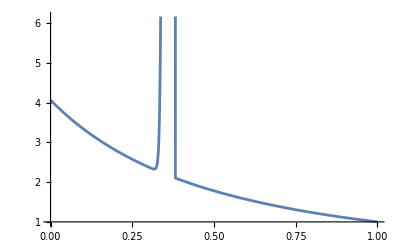
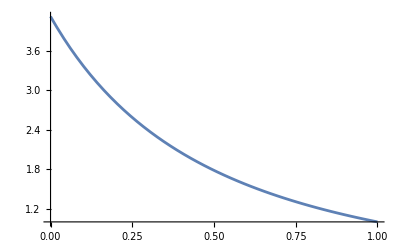
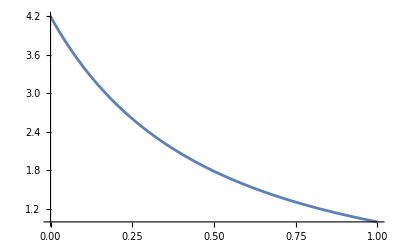
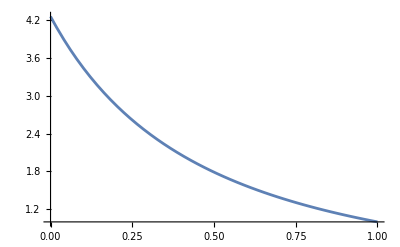
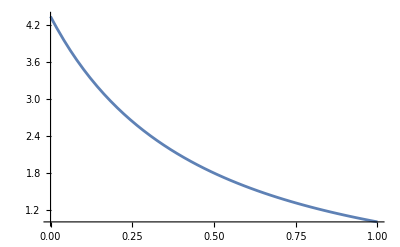
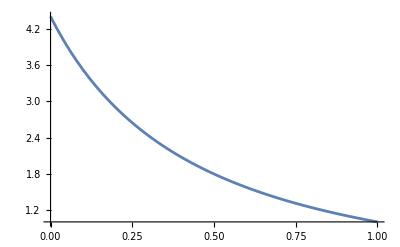
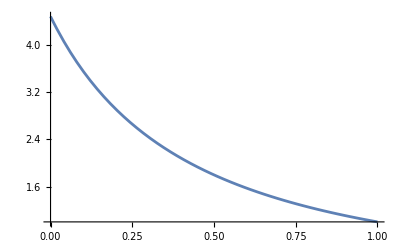
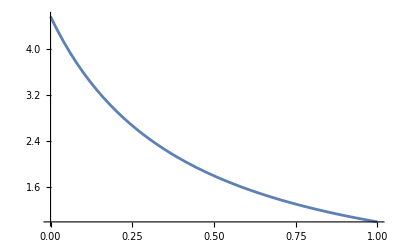

```mathematica
Table[Plot[Hypergeometric2F1[2,1/η,2/η,1-x],{x,0,1}],{η,0.01,0.1,0.01}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
FullSimplify[Limit[κpar0/κpar0 A0*(d-1)/(1+ΔPE/(κpar0*Tpar0)),{κpar0->Infinity},Assumptions->{A0>0,d>1,ΔPE∈Reals,Tpar0>0}],{A0>0,Tpar0>0,d>1}]
```

A0 (-1+d)

General::munfl: (1.4402×10^-207)/(«66») is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.97956×10^-205)/(«67») is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.4402×10^-207)/(«66») is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

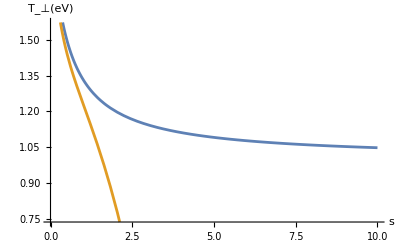
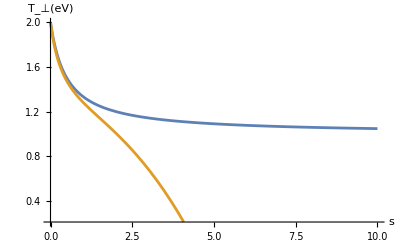
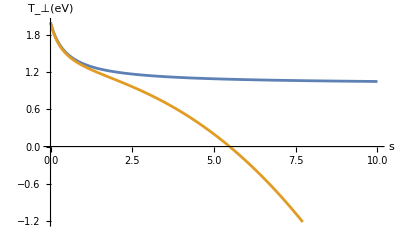
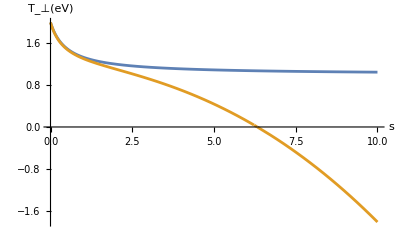
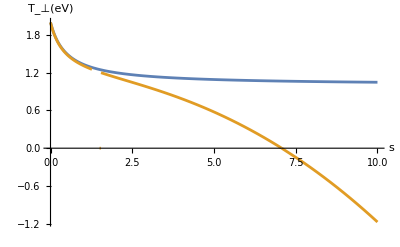
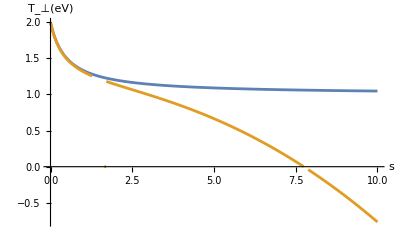
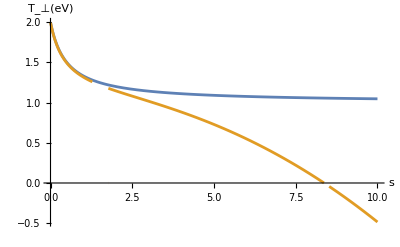
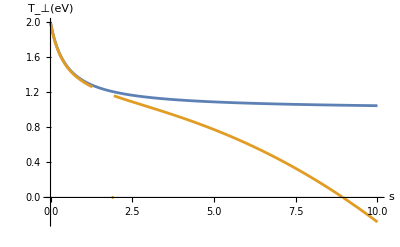

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
A0=2;
λ0=1;
Tpar0=1;
(*κpar0=2.;*)
κperp0[κpar0_]:=κpar0*λ0;
Tperp0=Tpar0*A0;
d[s_]:=s+1;
ΔPE[s_]:=-s^2;
δ[s_,κpar0_]:=λ0*A0*(d[s]-1)/(1+ΔPE[s]/(κpar0*Tpar0));




Tperpkappaproduct[s_,κpar0_]:=-((2 d[s] Tperp0 κperp0[κpar0] Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0[κpar0],1-δ[s,κpar0]] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0[κpar0],1-δ[s,κpar0]])/((-3+2 κpar0+2 κperp0[κpar0]) Hypergeometric2F1[2,1/2+κpar0,3/2+κpar0+κperp0[κpar0],1-δ[s,κpar0]]^2-2 (-1+2 κpar0+2 κperp0[κpar0]) Hypergeometric2F1[1,1/2+κpar0,3/2+κpar0+κperp0[κpar0],1-δ[s,κpar0]] Hypergeometric2F1[3,1/2+κpar0,3/2+κpar0+κperp0[κpar0],1-δ[s,κpar0]]))

Tperpanisomax[s_]:=Tperp0/(A0+(1-A0)*1/d[s])

Table[Plot[{Tperpanisomax[s],Tperpkappaproduct[s,κpar0]},{s,0.001,10},AxesLabel->{"s","T_⊥(eV)"}],{κpar0,10,100,10}]
```

```mathematica
Table[Plot[{Tperpanisomax[s],Tperpkappaproduct[s,κpar0]},{s,0.001,10},AxesLabel->{"s","T_⊥(eV)"}],{κpar0,100,1000,200}]
```

General::munfl: (6.21534×10^-260)/(«64») is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.58055×10^-257)/(«65») is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.21534×10^-260)/(«64») is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.